# Main Algorithms

```mathematica
dir=NotebookDirectory[];
img=ColorConvert[Import[dir<>"DRIVE/training/images/21_training.tif"],"Grayscale"];
imgData=ImageData[img];
```

```mathematica
img
```

-Graphics-

## Helper function

```mathematica
PNGtoGray[filename_]:=Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
GIFtoGray[filename_]:=255-Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
showGrayImage[img_]:=Graphics[Raster[img/Max[img]],Frame->False];
showBinaryImage[img_]:=Graphics[Raster[img],Frame->False];
showBinaryOverlay[img_,mask_]:=Graphics[Raster[MapThread[MapThread[If[#2==1,{1,0,0},{#1,#1,#1}]&,{#1,#2}]&,
{img,mask}]],Frame->False];
showGrayOverlay[img_,mask_]:=Graphics[{Raster[img/Max[img]],Raster[Map[Map[{#,0,0,If[#==1,.5,0]}&,#]&,mask]]},Frame->False];
```

## S_op

We remove noise while preserving most of the capillaries using geodesic reconstruction of the opened images into the original image S_0

Each structuring element L_i (every 15^□) is a 15-pixel long 1-pixel wide. Its size is approximately the range of the diameter of the biggest vessels for 512 × 512 × 8 images of retinal angiography.

In the image S_op, every isolated round and bright zone whose diameter is less than 15 pixels has been removed. Being a supremum of openings by reconstruction this operation is an opening, called linear opening by reconstruction of size 15.

S_op=γ_S_0^rec(Max_(i=1...12){γ_L_i(S_0)})

My question:
Is this equation means
	1. apply erosion with structure elements L_1... L_12 to S_0
	2. Find the maximum for every pixel
	3. apply geodesic opening with marker image being original image

γ_S_0^rec = geodesic opening
γ_S_0^rec(S) = sup_dϵlℕ (Δ_S_0^d(S))   // S_0= marker image

### Step 1: Construct L_i

```mathematica
angles=Table[{Cos[t],Sin[t]},{t,0,11π/12,π/12}]
```

{{1,0},{(1+√3)/(2 √2),(-1+√3)/(2 √2)},{(√3)/2,1/2},{1/(√2),1/(√2)},{1/2,(√3)/2},{(-1+√3)/(2 √2),(1+√3)/(2 √2)},{0,1},{-(-1+√3)/(2 √2),(1+√3)/(2 √2)},{-1/2,(√3)/2},{-1/(√2),1/(√2)},{-(√3)/2,1/2},{-(1+√3)/(2 √2),(-1+√3)/(2 √2)}}

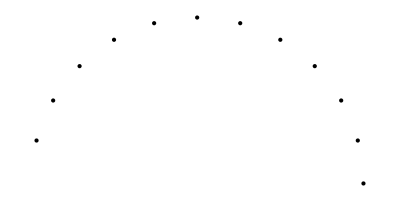

```mathematica
Graphics[{ Point[angles]}]
```

```mathematica
linearStrut=Table[Round[{Cos[t],Sin[t]}* #] &/@(Range[15]-8),{t,0,11π/12,π/12}]
```

{{{-7,0},{-6,0},{-5,0},{-4,0},{-3,0},{-2,0},{-1,0},{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0}},{{-7,-2},{-6,-2},{-5,-1},{-4,-1},{-3,-1},{-2,-1},{-1,0},{0,0},{1,0},{2,1},{3,1},{4,1},{5,1},{6,2},{7,2}},{{-6,-4},{-5,-3},{-4,-2},{-3,-2},{-3,-2},{-2,-1},{-1,0},{0,0},{1,0},{2,1},{3,2},{3,2},{4,2},{5,3},{6,4}},{{-5,-5},{-4,-4},{-4,-4},{-3,-3},{-2,-2},{-1,-1},{-1,-1},{0,0},{1,1},{1,1},{2,2},{3,3},{4,4},{4,4},{5,5}},{{-4,-6},{-3,-5},{-2,-4},{-2,-3},{-2,-3},{-1,-2},{0,-1},{0,0},{0,1},{1,2},{2,3},{2,3},{2,4},{3,5},{4,6}},{{-2,-7},{-2,-6},{-1,-5},{-1,-4},{-1,-3},{-1,-2},{0,-1},{0,0},{0,1},{1,2},{1,3},{1,4},{1,5},{2,6},{2,7}},{{0,-7},{0,-6},{0,-5},{0,-4},{0,-3},{0,-2},{0,-1},{0,0},{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{0,7}},{{2,-7},{2,-6},{1,-5},{1,-4},{1,-3},{1,-2},{0,-1},{0,0},{0,1},{-1,2},{-1,3},{-1,4},{-1,5},{-2,6},{-2,7}},{{4,-6},{3,-5},{2,-4},{2,-3},{2,-3},{1,-2},{0,-1},{0,0},{0,1},{-1,2},{-2,3},{-2,3},{-2,4},{-3,5},{-4,6}},{{5,-5},{4,-4},{4,-4},{3,-3},{2,-2},{1,-1},{1,-1},{0,0},{-1,1},{-1,1},{-2,2},{-3,3},{-4,4},{-4,4},{-5,5}},{{6,-4},{5,-3},{4,-2},{3,-2},{3,-2},{2,-1},{1,0},{0,0},{-1,0},{-2,1},{-3,2},{-3,2},{-4,2},{-5,3},{-6,4}},{{7,-2},{6,-2},{5,-1},{4,-1},{3,-1},{2,-1},{1,0},{0,0},{-1,0},{-2,1},{-3,1},{-4,1},{-5,1},{-6,2},{-7,2}}}

```mathematica
kernelFromStructure[structure_] := Block[
	{size = 2 Max @ Abs @ MinMax @ structure + 1},
	Transpose@ReplacePart[Table[0, size, size], Thread[Append[structure, {0, 0}] + (size + 1)/2 -> 1]]
]
```

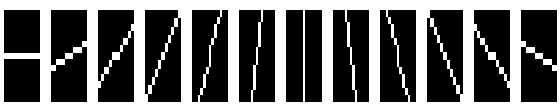

```mathematica
GraphicsRow[showBinaryImage[kernelFromStructure[#]]&/@linearStrut]
```

```mathematica
kernels=kernelFromStructure[#]&/@linearStrut
```

{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,1}},{{0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0}},{{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0}},{{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,1,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,1,1,1,1,0,0},{0,0,0,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

### Step 2: Applying Opening with L_i

```mathematica
AbsoluteTiming[erosionByLinearStrucImageList=Erosion[img,#]&/@kernels]
```

{0.919604,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
AbsoluteTiming[erosionByLinearStrucImageDataList=ImageData[#]&/@erosionByLinearStrucImageList]
```

{0.026732,{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}}
 |  |  |  |

```mathematica
maxErosion=MapThread[Max,erosionByLinearStrucImageDataList,2];
```

```mathematica
maskImage=Image[maxErosion]
```

-Graphics-

But the built-in GeodesicOpening doesn’t have imageMarker. 
Therefore, I implemented GeodesicOpening myself.

	γ_S_0^rec = geodesic opening
γ_S_0^rec(S) = sup_dϵlℕ (Δ_S_0^d(S))   // S_0= marker image

Pick the maximum until the Dilation doesn’t change

```mathematica
?GeodesicDilation
```

GeodesicDilation[marker,mask] gives the fixed point of the geodesic dilation of the marker constrained by the mask.

```mathematica
geodesicDilation[image_, marker_, 1]:=
```

```mathematica
geodesicOpening[marker_, mask_]:= FixedPointList[GeodesicDilation[#, mask]&, marker]
```

```mathematica
geodesicOpening[marker_, mask_]:= 
	MapThread[Max, ImageData/@ FixedPointList[GeodesicDilation[#, mask]&, marker], 2]
```

```mathematica
geodesicClosing[marker_, mask_]:=
```

```mathematica
markerImage=img;
```

```mathematica
geodesicDilationList=geodesicOpening[markerImage,maskImage]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
geodesicDilationImageDataList=ImageData/@geodesicDilationList
```

{{1},{1},{1}}
 |  |  |  |

```mathematica
AbsoluteTiming[SopData=geodesicOpening[markerImage, maskImage]]
```

{0.271236,{1}}
 |  |  |  |

```mathematica
Sop=Image[SopData]
```

-Graphics-

```mathematica
Dimensions/@{erosionByLinearStrucImageDataList}
```

{{12,584,565}}

```mathematica
AbsoluteTiming[topHatList=(SopData-#)&/@erosionByLinearStrucImageDataList]
```

{0.160054,{{1},{1},{1},{1},{1},{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,541,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},582,{1}},1,{1},{1},{1},{1},{1}}}
 |  |  |  |

```mathematica
AbsoluteTiming[SsumData=Total[topHatList]]
```

{0.011514,{1}}
 |  |  |  |

```mathematica
Ssum=Image[SsumData]
```

-Graphics-

This transformation (a sum of top hats) reduces small bright noise and improves the contrast of all linear parts. Vessels could be manually segmented with a simple threshold on S_sum

### Alternating Filter

```mathematica
?GaussianFilter
```

GaussianFilter[image,r] filters image by convolving with a Gaussian kernel of pixel radius r.
GaussianFilter[image,r,{n_1,n_2}] convolves image with a kernel formed from the n_i^th derivatives of the discrete Gaussian.
GaussianFilter[image,{r,σ},…]  uses a Gaussian kernel with radius r and standard deviation σ.
GaussianFilter[image,{{r_1,r_2},…}] uses radii r_i etc. in vertical and horizontal directions.
GaussianFilter[data,…] applies Gaussian filtering to an array of data.

```mathematica
GaussianFilter[Ssum, {7, 7/4}]
```

-Graphics-

```mathematica
Slap=LaplacianFilter[GaussianFilter[Ssum, {7, 7/4}],1]
```

-Graphics-

## Final Result

### S1

1. Apply Erosion with Linear Structure Element

```mathematica
SlapErosionByLinearStrucImageList=Erosion[Slap,#]&/@kernels;
```

2. Pick the Maximum pixel-wise

```mathematica
AbsoluteTiming[SlapErosionByLinearStrucImageDataList=ImageData[#]&/@SlapErosionByLinearStrucImageList]
```

{0.00004,{1}}
 |  |  |  |

```mathematica
slapMaxData=MapThread[Max,SlapErosionByLinearStrucImageDataList,2];
```

3. Apply GeodesicOpening

```mathematica
slapMax=Image[slapMaxData]
```

-Graphics-

```mathematica
S1Data=geodesicOpening[Slap,slapMax]
```

{1}
 |  |  |  |

```mathematica
S1=Image[S1Data]
```

-Graphics-

### S2

1. Apply Dilation with Linear Structure Element

```mathematica
SlapDilationByLinearStrucImageList=Dilation[S1,#]&/@kernels;
```

2. Pick the Maximum pixel-wise

```mathematica
AbsoluteTiming[SlapDilationByLinearStrucImageDataList=ImageData[#]&/@SlapDilationByLinearStrucImageList]
```

{0.00003,{1}}
 |  |  |  |

```mathematica
slapMinData=MapThread[Min,SlapDilationByLinearStrucImageDataList,2];
```

```mathematica
slapMin=Image[slapMinData]
```

-Graphics-

3. Apply GeodesicOpening with marker image = S1

```mathematica
S2Data=geodesicOpening[S1,slapMin]
```

{1}
 |  |  |  |

```mathematica
S2=Image[S2Data]
```

-Graphics-

### S_res

#### new linear struct e = 2

```mathematica
linearStrut30=Table[Round[{Cos[t],Sin[t]}* #] &/@(Range[30]-16),{t,0,11π/12,π/12}];
```

```mathematica
GraphicsRow[showBinaryImage[kernelFromStructure[#]]&/@linearStrut30]
```

-Graphics-

```mathematica
kernels30=kernelFromStructure[#]&/@linearStrut30;
```

#### 1. Erosion with L_i e = 2

```mathematica
erosionOnSres=Erosion[S2,#]&/@kernels30
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
erosionOnSresData=ImageData/@erosionOnSres;
```

#### 2. Pick maximum

```mathematica
erosionOnSresMaxData=MapThread[Max,erosionOnSresData,2];
```

```mathematica
Sres=Image[erosionOnSresMaxData]
```

-Graphics-

```mathematica
bin=Binarize[Sres,0.025]
```

-Graphics-

```mathematica
binData=ImageData[bin];
```

```mathematica
showGrayOverlay[imgData,binData]
```

-Graphics-